```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Math\Lags\ARlags.m;
```

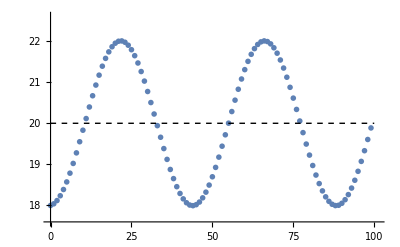

```mathematica
unitaryDiscrete = PriceSequenceGraphLags[{1, 0, 0, 0, 0, 0, 0, 0, 0},0.02,18,20,100,0.0001, False]
```

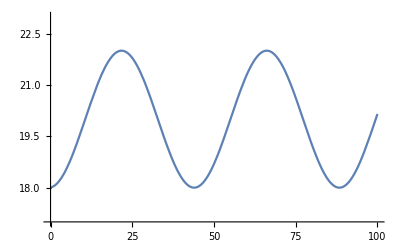

```mathematica
unitaryContinuous = Plot[20 - 2 * Cos[(0.02)^0.5  * (t + 0.5)], {t, 0, 100}, PlotRange -> {{0, 100}, {17, 23}}]
```

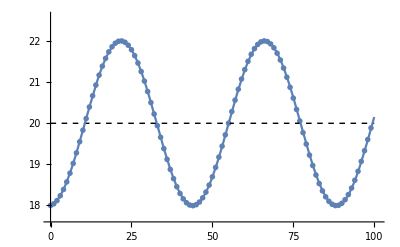

```mathematica
Show[unitaryDiscrete, unitaryContinuous]
```

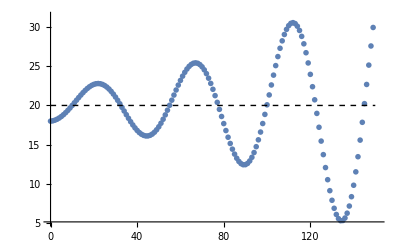

```mathematica
unstableDiscrete = PriceSequenceGraphLags[{1.03, 0, 0, 0, 0, 0, 0, 0, 0},0.02,18,20,150,0.00001, False]
```

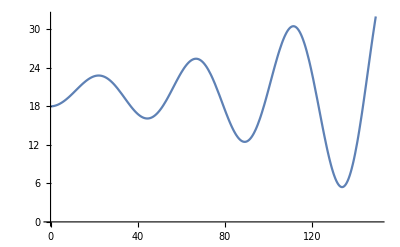

```mathematica
unstableContinuous = Plot[20 - E^{(1.02956-1)*(t + 1)/2}* 2 * Cos[(0.02 - 0.25 * (1.02956 - 1)^2)^0.5  * (t + 1)], {t, 0, 200}, PlotRange -> {{0, 150}, {0, 32}}]
```

```mathematica
E^0.02956
```

1.03

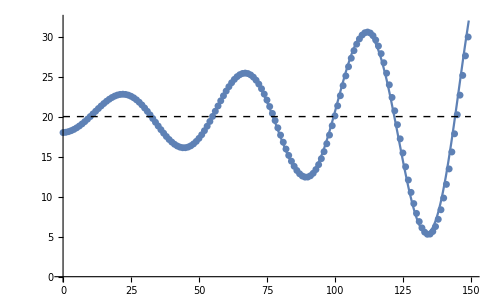

```mathematica
Show[unstableContinuous, unstableDiscrete]
```

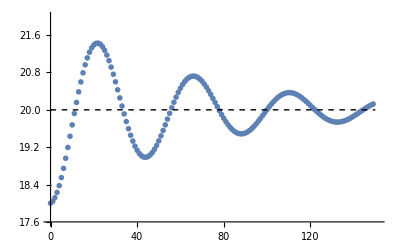

```mathematica
dampedDiscrete = PriceSequenceGraphLags[{0.97, 0, 0, 0, 0, 0, 0, 0, 0},0.02,18,20,150,0.0001, False]
```

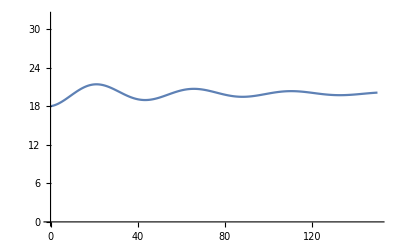

```mathematica
dampedContinuous = Plot[20 - E^{(0.969541-1)*(t + 0.5)/2}* 2 * Cos[(0.02 - 0.25 * (0.969541 - 1)^2)^0.5  * (t + 0.5)], {t, 0, 150}, PlotRange -> {{0, 150}, {0, 32}}]
```

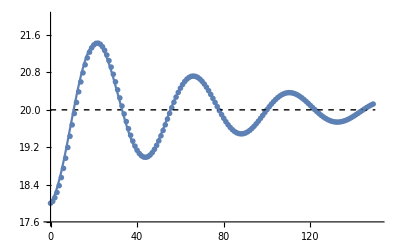

```mathematica
Show[dampedDiscrete, dampedContinuous]
```